## Definiciones

```mathematica
SetDirectory["/home/jadeleon/Documents/chaos_meets_channels/ja_files"];
```

```mathematica
Get["../Mathematica_packages/QMB.wl"]
```

```mathematica
LogSpace[start_,end_,n_]:=Exp@Subdivide[Log[start],Log[end],n-1]
```

## Cálculo

```mathematica
{t0,tf}={10.^-1,10.^3}
```

{0.1,1000.}

```mathematica
t=LogSpace[t0,tf,100];
```

```mathematica
Do[
{hz,J} = points[[j]];

(* Importar las matrices de Choi *)
chois=Table[ArrayReshape[#,{4,4}]&/@ToExpression[Import["~/Documents/chaos_meets_channels/ja_files/data/chois/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>"/"<>StringPadLeft[ToString[i],3,"0"]<>".csv"]],{i,100}];

(* Calcular la pureza de las matrices de Choi *)
purities=Chop[Map[Purity[#]&,chois,{2}]];

(* Calcular el promedio temporal de la pureza promedio de Choi de 0.1 a 1000 *)
tmpAvgChoiPurity=Table[
purityInterp = Interpolation[Transpose[{t,i}]]; 
NIntegrate[purityInterp[t],{t,t01,tf}]/(tf-t01)
,{i,purities}];
line1={Blue,Thickness[0.003],InfiniteLine[{{0.1,#},{100,#}}]&[Mean[tmpAvgChoiPurity]]};

(* Calcular el promedio temporal de la pureza promedio de Choi de 170.735 a 1000 (últimos 20 tiempos en la escala log) *)
tmpAvgChoiPurity2=Table[
purityInterp=Interpolation[Transpose[{LogSpace[t02,tf,20],i[[-20;;]]}]]; 
NIntegrate[purityInterp[t],{t,t02,tf}]/(tf-t02)
,{i,purities}];
line2={Orange,Thickness[0.003],InfiniteLine[{{0.1,#},{100,#}}]&[Mean[tmpAvgChoiPurity2]]};

{means,stdDevs}=Transpose[{Mean[#],StandardDeviation[#]}&/@Transpose[purities]];
data=Transpose[{LogSpace[0.1,1000,100],means}];

(*Convertir x a escala logarítmica*)
logData={Log10[#1],#2}&@@@data;
upper=logData+Transpose[{ConstantArray[0,Length[logData]],stdDevs/2}];
lower=logData-Transpose[{ConstantArray[0,Length[logData]],stdDevs/2}];

offset=0.03; (*Margen para evitar cortes en la parte superior*)

(*Generar las líneas de la cuadrícula en el rango 0.25 a 1. en pasos de 0.25*)
gridLines=Table[{GrayLevel[0.75],Dashed,Thickness[0.005],Opacity[0.75],InfiniteLine[{{0.1,y},{1,y}}]},{y,0.25,1,0.25}];

(*Crear la gráfica*)
fig=Graphics[{(*Agregar líneas de la cuadrícula*){Red,Polygon[Join[upper,Reverse[lower]]]},(*Región de incertidumbre*){Red,Line[logData]} (*Línea central*),line1,line2,gridLines},
PlotRange->{Automatic,{0.25-offset,1+offset}},
PlotLabel->Style["h_z = "<>ToString[NumberForm[hz,{Infinity,2}]]<>", "<>"J = "<>ToString[NumberForm[J,{Infinity,2}]]<>"",Black,FontSize->20],
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[Tr[HoldForm[𝒟]^2]]},
FrameTicks->{{Automatic,None},(*Ticks solo a la izquierda*){Table[{Log10[t],Superscript["10",Round[Log10[t]]]},{t,{0.1,1,10,100,1000}}],None (*Ticks solo abajo*)}},
AspectRatio->0.6,ImageSize->500];

Export["~/Documents/chaos_meets_channels/ja_files/figs_ja/choi/purity_dynamics/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>".pdf",fig,"PDF"];

,{j,lenpoints}]
```

```mathematica
avgOftmpAvgsOfChoiPurity2[[-1]]
```

{0.,0.333333,0.362796,0.0160861}

```mathematica
Mean[StandardDeviation[purities[[#,-20;;]]]&/@Range[100]]
```

0.0233849

```mathematica
fluctuaciones={};
Do[
{hz,J} = points[[j]];

(* Importar las matrices de Choi *)
chois=Table[ArrayReshape[#,{4,4}]&/@ToExpression[Import["~/Documents/chaos_meets_channels/ja_files/data/chois/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>"/"<>StringPadLeft[ToString[i],3,"0"]<>".csv"]],{i,100}];

(* Calcular la pureza de las matrices de Choi *)
purities=Chop[Map[Purity[#]&,chois,{2}]];

(* Flucuationes promedio *)
AppendTo[fluctuaciones,{hz,J,Mean[StandardDeviation[purities[[#,-20;;]]]&/@Range[100]]}];

,{j,lenpoints}]
```

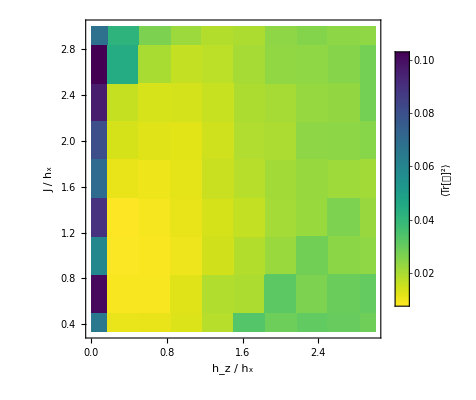

```mathematica
ListDensityPlot[Select[fluctuaciones,#[[2]]!=0.&],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->Full,
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨"<>ToString[TraditionalForm[HoldForm[Tr[HoldForm[𝒟]]^2]]]<>"⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

## Revisando algo

```mathematica
t=LogSpace[0.1,1000,100]
```

{0.1,0.10975,0.12045,0.132194,0.145083,0.159228,0.174753,0.191791,0.21049,0.231013,0.253536,0.278256,0.305386,0.33516,0.367838,0.403702,0.443062,0.48626,0.53367,0.585702,0.642807,0.70548,0.774264,0.849753,0.932603,1.02353,1.12332,1.23285,1.35305,1.48497,1.62975,1.78865,1.96304,2.15443,2.36449,2.59502,2.84804,3.12572,3.43047,3.76494,4.13201,4.53488,4.97702,5.46228,5.99484,6.57933,7.22081,7.92483,8.69749,9.54548,10.4762,11.4976,12.6186,13.8489,15.1991,16.681,18.3074,20.0923,22.0513,24.2013,26.5609,29.1505,31.9927,35.1119,38.5353,42.2924,46.4159,50.9414,55.9081,61.3591,67.3415,73.9072,81.1131,89.0215,97.701,107.227,117.681,129.155,141.747,155.568,170.735,187.382,205.651,225.702,247.708,271.859,298.365,327.455,359.381,394.421,432.876,475.081,521.401,572.237,628.029,689.261,756.463,830.218,911.163,1000.}

```mathematica
points=Complement[Tuples[Subdivide[0.,3.,9],2],Join[{#},{0.}]&/@Subdivide[0.,3.,9]]
lenpoints=Length[points]
```

{{0.,0.333333},{0.,0.666667},{0.,1.},{0.,1.33333},{0.,1.66667},{0.,2.},{0.,2.33333},{0.,2.66667},{0.,3.},{0.333333,0.333333},{0.333333,0.666667},{0.333333,1.},{0.333333,1.33333},{0.333333,1.66667},{0.333333,2.},{0.333333,2.33333},{0.333333,2.66667},{0.333333,3.},{0.666667,0.333333},{0.666667,0.666667},{0.666667,1.},{0.666667,1.33333},{0.666667,1.66667},{0.666667,2.},{0.666667,2.33333},{0.666667,2.66667},{0.666667,3.},{1.,0.333333},{1.,0.666667},{1.,1.},{1.,1.33333},{1.,1.66667},{1.,2.},{1.,2.33333},{1.,2.66667},{1.,3.},{1.33333,0.333333},{1.33333,0.666667},{1.33333,1.},{1.33333,1.33333},{1.33333,1.66667},{1.33333,2.},{1.33333,2.33333},{1.33333,2.66667},{1.33333,3.},{1.66667,0.333333},{1.66667,0.666667},{1.66667,1.},{1.66667,1.33333},{1.66667,1.66667},{1.66667,2.},{1.66667,2.33333},{1.66667,2.66667},{1.66667,3.},{2.,0.333333},{2.,0.666667},{2.,1.},{2.,1.33333},{2.,1.66667},{2.,2.},{2.,2.33333},{2.,2.66667},{2.,3.},{2.33333,0.333333},{2.33333,0.666667},{2.33333,1.},{2.33333,1.33333},{2.33333,1.66667},{2.33333,2.},{2.33333,2.33333},{2.33333,2.66667},{2.33333,3.},{2.66667,0.333333},{2.66667,0.666667},{2.66667,1.},{2.66667,1.33333},{2.66667,1.66667},{2.66667,2.},{2.66667,2.33333},{2.66667,2.66667},{2.66667,3.},{3.,0.333333},{3.,0.666667},{3.,1.},{3.,1.33333},{3.,1.66667},{3.,2.},{3.,2.33333},{3.,2.66667},{3.,3.}}

90

```mathematica
Do[
{hz,J} = points[[j]];

(* Importar las matrices de Choi *)
chois=Table[ArrayReshape[#,{4,4}]&/@ToExpression[Import["~/Documents/chaos_meets_channels/ja_files/data/chois/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>"/"<>StringPadLeft[ToString[i],3,"0"]<>"_2.csv"]],{i,100}];

(* Calcular la pureza de las matrices de Choi *)
purities=Chop[Map[Purity[#]&,chois,{2}]];

(* Calcular el promedio temporal de la pureza promedio de Choi de 0.1 a 1000 *)
tmpAvgChoiPurity=Table[
purityInterp = Interpolation[Transpose[{t,i}]]; 
NIntegrate[purityInterp[t],{t,t01,tf}]/(tf-t01)
,{i,purities}];
line1={Blue,Thickness[0.003],InfiniteLine[{{0.1,#},{100,#}}]&[Mean[tmpAvgChoiPurity]]};

(* Calcular el promedio temporal de la pureza promedio de Choi de 170.735 a 1000 (últimos 20 tiempos en la escala log) *)
tmpAvgChoiPurity2=Table[
purityInterp=Interpolation[Transpose[{LogSpace[t02,tf,20],i[[-20;;]]}]]; 
NIntegrate[purityInterp[t],{t,t02,tf}]/(tf-t02)
,{i,purities}];
line2={Orange,Thickness[0.003],InfiniteLine[{{0.1,#},{100,#}}]&[Mean[tmpAvgChoiPurity2]]};

{means,stdDevs}=Transpose[{Mean[#],StandardDeviation[#]}&/@Transpose[purities]];
data=Transpose[{LogSpace[0.1,1000,100],means}];

(*Convertir x a escala logarítmica*)
logData={Log10[#1],#2}&@@@data;
upper=logData+Transpose[{ConstantArray[0,Length[logData]],stdDevs/2}];
lower=logData-Transpose[{ConstantArray[0,Length[logData]],stdDevs/2}];

offset=0.03; (*Margen para evitar cortes en la parte superior*)

(*Generar las líneas de la cuadrícula en el rango 0.25 a 1. en pasos de 0.25*)
gridLines=Table[{GrayLevel[0.75],Dashed,Thickness[0.005],Opacity[0.75],InfiniteLine[{{0.1,y},{1,y}}]},{y,0.25,1,0.25}];

(*Crear la gráfica*)
fig=Graphics[{(*Agregar líneas de la cuadrícula*){Red,Polygon[Join[upper,Reverse[lower]]]},(*Región de incertidumbre*){Red,Line[logData]} (*Línea central*),line1,line2,gridLines},
PlotRange->{Automatic,{0.25-offset,1+offset}},
PlotLabel->Style["h_z = "<>ToString[NumberForm[hz,{Infinity,2}]]<>", "<>"J = "<>ToString[NumberForm[J,{Infinity,2}]]<>"",Black,FontSize->20],
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{TraditionalForm[HoldForm[J]*HoldForm[t]],TraditionalForm[Tr[HoldForm[𝒟]^2]]},
FrameTicks->{{Automatic,None},(*Ticks solo a la izquierda*){Table[{Log10[t],Superscript["10",Round[Log10[t]]]},{t,{0.1,1,10,100,1000}}],None (*Ticks solo abajo*)}},
AspectRatio->0.6,ImageSize->500];

Export["~/Documents/chaos_meets_channels/ja_files/figs_ja/choi/purity_dynamics/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>"_2.pdf",fig,"PDF"];

,{j,lenpoints}]
```

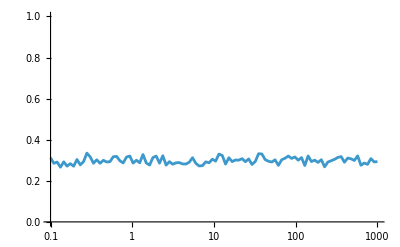

```mathematica
ListLogLinearPlot[Transpose[{LogSpace[0.1,1000,100],purities[[1]]}],PlotRange->{{0.1,1000},{0,1}},Joined->True]
```

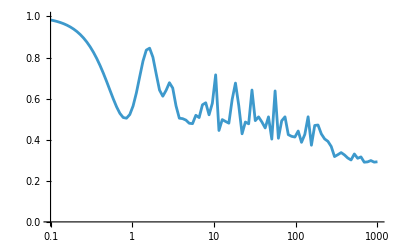

```mathematica
ListLogLinearPlot[Transpose[{LogSpace[0.1,1000,100],purities[[1]]}],PlotRange->{{0.1,1000},{0,1}},Joined->True]
```

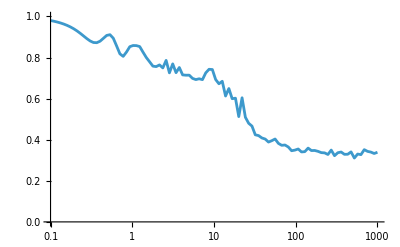

```mathematica
ListLogLinearPlot[Transpose[{LogSpace[0.1,1000,100],purities[[1]]}],PlotRange->{{0.1,1000},{0,1}},Joined->True]
```

```mathematica
hz=1.33;J=3.00;

(* Importar las matrices de Choi *)
chois=Table[ArrayReshape[#,{4,4}]&/@ToExpression[Import["~/Documents/chaos_meets_channels/ja_files/data/chois/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>"/"<>StringPadLeft[ToString[i],3,"0"]<>"_2.csv"]],{i,100}];

(* Calcular la pureza de las matrices de Choi *)
purities=Chop[Map[Purity[#]&,chois,{2}]];
```

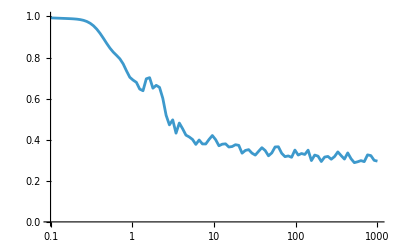

```mathematica
ListLogLinearPlot[Transpose[{LogSpace[0.1,1000,100],purities[[3]]}],PlotRange->{{0.1,1000},{0,1}},Joined->True]
```

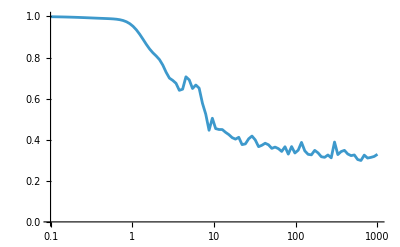

```mathematica
ListLogLinearPlot[Transpose[{LogSpace[0.1,1000,100],purities[[3]]}],PlotRange->{{0.1,1000},{0,1}},Joined->True]
```

## Haar

```mathematica
points=Tuples[Subdivide[0.05,2.95,9],2]
```

{{0.05,0.05},{0.05,0.372222},{0.05,0.694444},{0.05,1.01667},{0.05,1.33889},{0.05,1.66111},{0.05,1.98333},{0.05,2.30556},{0.05,2.62778},{0.05,2.95},{0.372222,0.05},{0.372222,0.372222},{0.372222,0.694444},{0.372222,1.01667},{0.372222,1.33889},{0.372222,1.66111},{0.372222,1.98333},{0.372222,2.30556},{0.372222,2.62778},{0.372222,2.95},{0.694444,0.05},{0.694444,0.372222},{0.694444,0.694444},{0.694444,1.01667},{0.694444,1.33889},{0.694444,1.66111},{0.694444,1.98333},{0.694444,2.30556},{0.694444,2.62778},{0.694444,2.95},{1.01667,0.05},{1.01667,0.372222},{1.01667,0.694444},{1.01667,1.01667},{1.01667,1.33889},{1.01667,1.66111},{1.01667,1.98333},{1.01667,2.30556},{1.01667,2.62778},{1.01667,2.95},{1.33889,0.05},{1.33889,0.372222},{1.33889,0.694444},{1.33889,1.01667},{1.33889,1.33889},{1.33889,1.66111},{1.33889,1.98333},{1.33889,2.30556},{1.33889,2.62778},{1.33889,2.95},{1.66111,0.05},{1.66111,0.372222},{1.66111,0.694444},{1.66111,1.01667},{1.66111,1.33889},{1.66111,1.66111},{1.66111,1.98333},{1.66111,2.30556},{1.66111,2.62778},{1.66111,2.95},{1.98333,0.05},{1.98333,0.372222},{1.98333,0.694444},{1.98333,1.01667},{1.98333,1.33889},{1.98333,1.66111},{1.98333,1.98333},{1.98333,2.30556},{1.98333,2.62778},{1.98333,2.95},{2.30556,0.05},{2.30556,0.372222},{2.30556,0.694444},{2.30556,1.01667},{2.30556,1.33889},{2.30556,1.66111},{2.30556,1.98333},{2.30556,2.30556},{2.30556,2.62778},{2.30556,2.95},{2.62778,0.05},{2.62778,0.372222},{2.62778,0.694444},{2.62778,1.01667},{2.62778,1.33889},{2.62778,1.66111},{2.62778,1.98333},{2.62778,2.30556},{2.62778,2.62778},{2.62778,2.95},{2.95,0.05},{2.95,0.372222},{2.95,0.694444},{2.95,1.01667},{2.95,1.33889},{2.95,1.66111},{2.95,1.98333},{2.95,2.30556},{2.95,2.62778},{2.95,2.95}}

```mathematica
Position[Round[points,10.^-2],{1.34,1.02}]
```

{{44}}

```mathematica
Do[
haarAvgdChoiPurity=Import["data/haar_avg_choi_purity/wisniacki/open/L_7/hx_1_hz_"<>ToString[NumberForm[i[[1]],{Infinity,2}]]<>"_J_"<>ToString[NumberForm[i[[2]],{Infinity,2}]]<>".csv","CSV"][[2;;]];

fig=ListLogLinearPlot[haarAvgdChoiPurity,
Joined->True,
PlotMarkers->{Automatic,9},
PlotStyle->Directive[Thickness[0.002]],
Frame->True,
FrameStyle->Directive[Black,FontSize->21],
FrameLabel->{HoldForm[J*t],"⟨ "<>ToString[TraditionalForm[Tr[HoldForm[𝒟]^2]]]<>" \!\(\*SubscriptBox[\(⟩\), \(Haar\)]\)"},
PlotLabel->Style["hz = "<>ToString[NumberForm[i[[1]],{Infinity,2}]]<>", J ="<>ToString[NumberForm[i[[2]],{Infinity,2}]],Black,FontSize->21],
ImageSize->450
];

Export["figs_ja/haarAvgd_ChoiPurity/wisniacki_L_7_hx_1_hz_"<>ToString[NumberForm[i[[1]],{Infinity,2}]]<>"_J_"<>ToString[NumberForm[i[[2]],{Infinity,2}]]<>".pdf",fig];
,{i,points}]
```